{-0.794788,-0.123127,0.0410425,0.0410425}

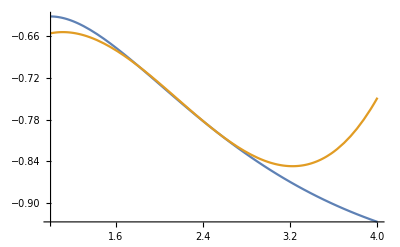

0.0862316

0.0287439

```mathematica
(*Problem #1*)
f[x_] := x*E^(-x)-1;
d={};
For[k=0,k≤3,k++,
AppendTo[d,D[f[x],{x,k}]/.x->2.5];
];
t[x_]:=d[[1]]+d[[2]](x-2.5)+d[[3]](x-2.5)^2+d[[4]](x-2.5)^3;
Plot[{f[x],t[x]},{x,1,4}]

normerror = Sqrt[Integrate[(f[x]-t[x])^2,{x,1,4}]];
meannormerror = normerror/(4-1);
Print[normerror];
Print[meannormerror];
```

-0.628323+0.0660124 x-0.0813614 x^2+0.0115519 x^3

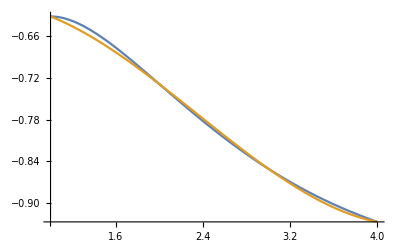

0.00748051

0.0024935

-3.05624×10^-7

```mathematica
(*Problem #2*)
f[x_] := x*E^(-x)-1;
xvals = {1,2,3,4};
yvals={};
For[k=1,k≤4,k++,
AppendTo[yvals,N[f[xvals[[k]]]]];
];
Vandermonde={};
For[i=1,i≤4,i++,
row={};
For[j=0,j≤3,j++,
AppendTo[row, xvals[[i]]^j];
];
AppendTo[Vandermonde,row];
];
coef=LinearSolve[Vandermonde,yvals];
p[x_]:=coef[[1]]+coef[[2]]x+coef[[3]]x^2+coef[[4]]x^3;
Print[p[x]];
(*Part B*)
Plot[{f[x],p[x]},{x,1,4}]
(*Part C*)
normerror = Sqrt[Integrate[(f[x]-p[x])^2,{x,1,4}]];
meannormerror = normerror/(4-1);
Print[normerror];
Print[meannormerror];
(*Part D*)
(*p(x) appears to be a much better approximation of f(x),
  as seen in the graphs and the fact that the mean error is a factor of 10 less
 than that in the taylor polynomial interpolation*)

(*Part E*)
d[x_]:=D[f[x],{x,4}];
M = FindMaxValue[{d[x],1≤x≤4},x];
errorbound = (M*(4-1)^(4))/Factorial[4];
Print[errorbound];
```

1-(3 x^2)/5+x^4/10

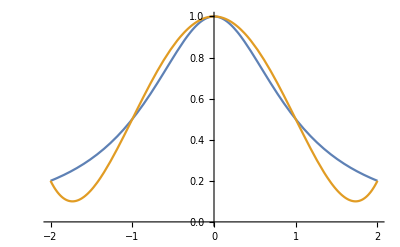

0.17052

0.04263

```mathematica
(*Problem #3*)
f[x_] :=1/(1+x^2);
xvals = {-2,-1,0,1,2};
yvals={};
For[k=1,k≤5,k++,
AppendTo[yvals,f[xvals[[k]]]];
];
Vandermonde={};
For[i=1,i≤5,i++,
row={1};
For[j=1,j≤4,j++,
AppendTo[row, xvals[[i]]^j];
];
AppendTo[Vandermonde,row];
];
coef=LinearSolve[Vandermonde,yvals];
p[x_]:=coef[[1]]+coef[[2]]x+coef[[3]]x^2+coef[[4]]x^3+coef[[5]]x^4;

Print[p[x]];
Plot[{f[x],p[x]},{x,-2,2}]

normerror = N[Sqrt[Integrate[(f[x]-p[x])^2,{x,-2,2}]]];
meannormerror = normerror/(2-(-2));
Print[normerror];
Print[meannormerror];
```